```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=amplitude*E^(steepness(x-wavespeed t -center)^2)+offset
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
D[q[τ,ξ],τ]/.{τ->t,ξ->x}
D[q[τ,ξ],ξ]/.{τ->t,ξ->x}
D[q[τ,ξ],{ξ,2}]/.{τ->t,ξ->x}
D[q[τ,ξ],{ξ,3}]/.{τ->t,ξ->x}
D[q[τ,ξ],{ξ,4}]/.{τ->t,ξ->x}
```

-2 amplitude ⅇ^(steepness (-center-t wavespeed+x)^2) steepness wavespeed (-center-t wavespeed+x)

2 amplitude ⅇ^(steepness (-center-t wavespeed+x)^2) steepness (-center-t wavespeed+x)

amplitude (2 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness+4 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness^2 (-center-t wavespeed+x)^2)

amplitude (12 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness^2 (-center-t wavespeed+x)+8 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness^3 (-center-t wavespeed+x)^3)

amplitude (12 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness^2+48 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness^3 (-center-t wavespeed+x)^2+16 ⅇ^(steepness (-center-t wavespeed+x)^2) steepness^4 (-center-t wavespeed+x)^4)

```mathematica
D[q[t, x], t] + D[q[t,x]^2-q[t,x]^3,x]//Simplify
```

1/5 ⅇ^(-30 (t+30 (-1/2+x)^2)) (-36+ⅇ^(20 (t+30 (-1/2+x)^2)) (41-102 x)+72 x-84 ⅇ^(10 (t+30 (-1/2+x)^2)) (-1+2 x))

```mathematica
D[q[t,x],t]
```

-2 ⅇ^(-10 t-300 (-1/2+x)^2)

```mathematica
D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

1/5 (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^3 (120000 ⅇ^(-100 (-1/2+x)^2)-48000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^2+1600000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^4)-24 ⅇ^(-100 (-1/2+x)^2) (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^2 (120000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)-8000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^3) (-1/2+x)

```mathematica
D[q[t,x],t]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

2 ⅇ^(-40 (t+30 (-1/2+x)^2)) (648 ⅇ^(20 (t+30 (-1/2+x)^2)) (14551-118200 x+358200 x^2-480000 x^3+240000 x^4)+1296 ⅇ^(10 (t+30 (-1/2+x)^2)) (21901-177600 x+537600 x^2-720000 x^3+360000 x^4)+864 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (777707-6350400 x+19310400 x^2-25920000 x^3+12960000 x^4))

```mathematica
D[q[t,x],t] +D[q[t,x]^2-q[t,x]^3,x]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

1/5 ⅇ^(-40 (t+30 (-1/2+x)^2)) (8640 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (7777121-63504102 x+193104000 x^2-259200000 x^3+129600000 x^4)+12 ⅇ^(20 (t+30 (-1/2+x)^2)) (7857547-63828014 x+193428000 x^2-259200000 x^3+129600000 x^4)+36 ⅇ^(10 (t+30 (-1/2+x)^2)) (7884359-63935998 x+193536000 x^2-259200000 x^3+129600000 x^4))

```mathematica
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
```

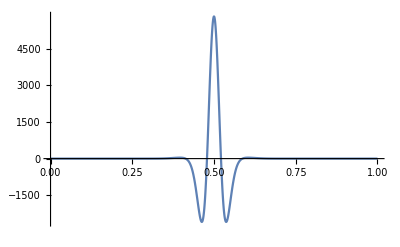

```mathematica
Plot[f[0,x],{x,0,1},PlotRange->All]
```

```mathematica
f[t,x]-D[q[t,x],t]-D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

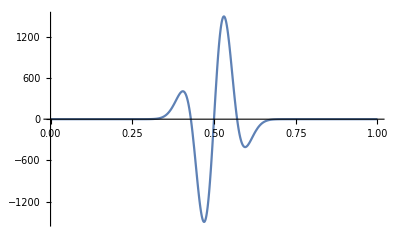

```mathematica
g[t_,x_]:=-D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
Plot[D[q[.1,ξ],{ξ,3}]/.{ξ->x},{x,0,1},PlotRange->All]
```

```mathematica
f[t,x]//Simplify
```

2 ⅇ^(-40 (t+30 (-1/2+x)^2)) (648 ⅇ^(20 (t+30 (-1/2+x)^2)) (14551-118200 x+358200 x^2-480000 x^3+240000 x^4)+1296 ⅇ^(10 (t+30 (-1/2+x)^2)) (21901-177600 x+537600 x^2-720000 x^3+360000 x^4)+864 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (777707-6350400 x+19310400 x^2-25920000 x^3+12960000 x^4))

```mathematica
D[h[ξ]^3 D[h[ξ],{ξ,3}],ξ]
```

3 h[ξ]^2 h'[ξ] h^(3)[ξ]+h[ξ]^3 h^(4)[ξ]

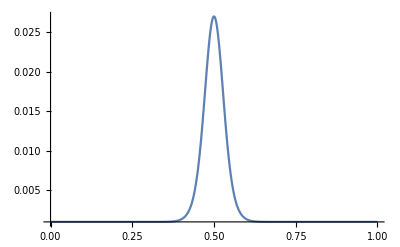

```mathematica
Plot[q[0,x]^3,{x,0,1},PlotRange->All]
```

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=amplitude*Sin[2π*wavenumber*(x - wavespeed*t)]+offset
D[q[τ,ξ],τ]/.{τ->t,ξ->x}
D[q[τ,ξ],ξ]/.{τ->t,ξ->x}
D[q[τ,ξ],{ξ,3}]/.{τ->t,ξ->x}
D[q[τ,ξ],{ξ,4}]/.{τ->t,ξ->x}
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
f[t,x]
```

-2 amplitude π wavenumber wavespeed Cos[2 π wavenumber (-t wavespeed+x)]

2 amplitude π wavenumber Cos[2 π wavenumber (-t wavespeed+x)]

-8 amplitude π^3 wavenumber^3 Cos[2 π wavenumber (-t wavespeed+x)]

16 amplitude π^4 wavenumber^4 Sin[2 π wavenumber (-t wavespeed+x)]

-2 amplitude π wavenumber wavespeed Cos[2 π wavenumber (-t wavespeed+x)]-48 amplitude^2 π^4 wavenumber^4 Cos[2 π wavenumber (-t wavespeed+x)]^2 (offset+amplitude Sin[2 π wavenumber (-t wavespeed+x)])^2+16 amplitude π^4 wavenumber^4 Sin[2 π wavenumber (-t wavespeed+x)] (offset+amplitude Sin[2 π wavenumber (-t wavespeed+x)])^3

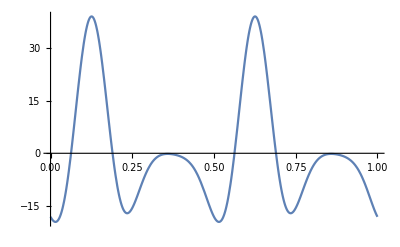

```mathematica
Plot[f[0,x],{x,0,1}]
```

```mathematica
Clear[amplitude, wavenumber,wavespeed, offset]
```

```mathematica
D[q[τ,ξ],τ]/.{τ->t,ξ->x}
```

-2 amplitude π wavenumber wavespeed Cos[2 π wavenumber (-t wavespeed+x)]

```mathematica
D[q[τ,ξ],ξ]/.{τ->t,ξ->x}
```

2 amplitude π wavenumber Cos[2 π wavenumber (-t wavespeed+x)]

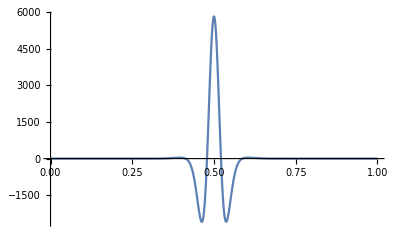

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=2/10*E^(-300(x-t-1/2)^2)+1/10
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
Plot[f[0,x],{x,0,1},PlotRange->All]
```

```mathematica
f[t,x]//Simplify
```

60 ⅇ^(-300 (1+2 t-2 x)^2) (3600 ⅇ^(225 (1+2 t-2 x)^2) (1/10+1/5 ⅇ^(-75 (1+2 t-2 x)^2))^3 (1-300 (1+2 t-2 x)^2+7500 (1+2 t-2 x)^4)+ⅇ^(225 (1+2 t-2 x)^2) (-1-2 t+2 x)+3240 (2+ⅇ^(75 (1+2 t-2 x)^2))^2 (1+2 t-2 x)^2 (49+200 t^2-200 x+200 x^2-200 t (-1+2 x)))

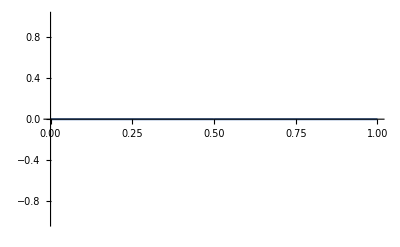

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=-0.2HeavisideTheta[x-t-1/2]+0.3
f[t_,x_]:=D[q[τ,ξ],τ]+D[q[τ,ξ]^3 D[q[τ,ξ],{ξ,3}],ξ]/.{τ->t,ξ->x}
Plot[f[0,x],{x,0,1},PlotRange->All]
```

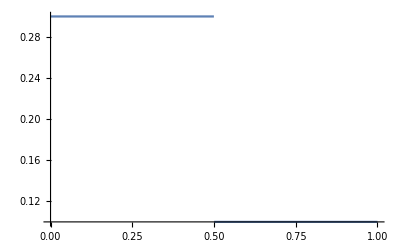

```mathematica
Plot[q[0,x],{x,0,1}]
```

```mathematica
f[t,x]
```

0.4 DiracDelta[-1-2 t+2 x]+1.92 DiracDelta[-1-2 t+2 x] (0.3-0.2 HeavisideTheta[-1/2-t+x])^2 DiracDelta''[-1-2 t+2 x]-3.2 (0.3-0.2 HeavisideTheta[-1/2-t+x])^3 DiracDelta^(3)[-1-2 t+2 x]